```mathematica
mpi0    = 0.1349764 ;
mp           = 0.93827231 ;
Ebeam      = 5.75;
Eb=Ebeam;

(*
* 6.2059,0.8019,-0.1064,1.8361,0.00,
* 94.6402,3.4433,-1.9773,-0.1315,0.0000,16.9977,2.1240,
*)
p1=6.2059;
p2=0.8019;
p3=-0.1064;
p4=1.836;
p5=0.0;

p6=94.6402 
p7=3.4433;
p8=-1.9773;
p9=-0.1315;
p10=0.0;
p11=16.9977;
p12=2.1240;

ALPHA=0.00729927;
Hc2=389379.36;
ksi[Q2_,x_]:=x/(2-x)*(1+mp^2/Q2);
W[Q2_,x_]:=Sqrt[Q2*(1/x-1)+mp^2];
E1CM[Q2_,x_]:=(W[Q2,x]^2+Q2+mp^2)/(2*W[Q2,x]);
E3CM[Q2_,x_]:=(W[Q2,x]^2-mpi0^2+mp^2)/(2*W[Q2,x]);
P1CM[Q2_,x_]:= Sqrt[E1CM[Q2,x]^2-mp^2];
P3CM[Q2_,x_]:= Sqrt[E3CM[Q2,x]^2-mp^2];
y[Q2_,x_,E_]:=Q2/(2*mp*x*E);
E1[Q2_,x_,E]:=Q2/(4*E^2);

tmin[Q2_,x_]:=-((Q2+mpi0^2)^2/4/W[Q2,x]^2-(P1CM[Q2,x]-P3CM[Q2,x])^2);
PHASE1[Q2_,x_]:=16*Pi*(W[Q2,x]^2-mp^2)*Sqrt[W[Q2,x]^4+Q2^2+mp^4+2*W[Q2,x]^2*Q2-2*W[Q2,x]^2*mp^2+2*Q2*mp^2];
PHASE2[Q2_,x_]:=16*Pi*(W[Q2,x]^2-mp^2)*Sqrt[W[Q2,x]^4+0.0     +mp^4+2*W[Q2,x]^2*Q2-2*W[Q2,x]^2*mp^2+2*Q2*mp^2];
PHASE[Q2_,x_]:=PHASE1[Q2,x];
HT[t_,Q2_,x_]:=p1*Exp[(p2+p3*(Log[x]-Log[0.15]))*t]*Q2^(p4/2.);
ET[t_,Q2_,x_]:=p6*Exp[(p7+p8*(Log[x]-Log[0.15]))*t]*Q2^(p9/2.);
HTEBAR[t_,Q2_,x_]:=p11*Exp[p12*t];

sTT[t_,Q2_,x_]:=If[-t>tmin[Q2,x],-Hc2*4*Pi*ALPHA/2/PHASE[Q2,x]/Q2^2*((-t-tmin[Q2,x])/8/mp^2*ET[t,Q2,x]^2),0.0];
(*sT[t_,Q2_,x_]:= If[-t>tmin[Q2,x]&&3.0>Q2>1.3&&x>0.09,    *)
sT[t_,Q2_,x_]:= If[-t>tmin[Q2,x]&&x>0.0,  Hc2*4*Pi*ALPHA/2/PHASE[Q2,x]/Q2^2*((1-ksi[Q2,x]^2)*HT[t,Q2,x]^2+(-t-tmin[Q2,x])/8/mp^2*ET[t,Q2,x]^2),.0];
sT1[t_,Q2_,x_]:= If[-t>tmin[Q2,x],    Hc2*4*Pi*ALPHA/2/PHASE[Q2,x]/Q2^2*((1-ksi[Q2,x]^2)*HT[t,Q2,x]^2+0*(-t-tmin[Q2,x])/8/mp^2*ET[t,Q2,x]^2),0.0];
sT2[t_,Q2_,x_]:= If[-t>tmin[Q2,x],    Hc2*4*Pi*ALPHA/2/PHASE[Q2,x]/Q2^2*(0*(1-ksi[Q2,x]^2)*HT[t,Q2,x]^2+(-t-tmin[Q2,x])/8/mp^2*ET[t,Q2,x]^2),0.0];
sLT[t_,Q2_,x_]:=If[-t>tmin[Q2,x],Hc2*4.*Pi*ALPHA/Sqrt[2.]/PHASE[Q2,x]/Q2^1.5*ksi[Q2,x]*Sqrt[1.-ksi[Q2,x]^2]*Sqrt[-t-tmin[Q2,x]]/2/mp*HTEBAR[t,Q2,x]^2,0.0];
sL[t_,Q2_,x_]:=0.0;
eps1[Q2_,x_,E_]:=(1-y[Q2,x,E]-Q2/(4*E^2))/(1-y[Q2,x,E]+y[Q2,x,E]^2/2+Q2/(4*E^2));
eps[Q2_,x_,E_]:=If[eps1[Q2,x,E]>0.0,(1-y[Q2,x,E]-Q2/(4*E^2))/(1-y[Q2,x,E]+y[Q2,x,E]^2/2+Q2/(4*E^2)),0.0];
sU[t_,Q2_,x_,E_]:=sT[t,Q2,x]+eps[Q2,x,E]*sL[t,Q2,x];
(*Plot[{sU[-t,2.,0.2,Ebeam]},{t,0.,2.}]*)
(*---------------------------------------------------*)
sTmin[t_,Q2_,x_]=-sTT[t,Q2,x];
sLmax[t_,Q2_,x_]=If[eps1[Q2,x,Ebeam]>0.001,(sU[t,Q2,x,Ebeam]-sTmin[t,Q2,x])/eps[Q2,x,Ebeam],0.0];
(*---------------------------------------------------*)
sTn[t_,Q2_,x_]:=0.0;
sLn[t_,Q2_,x_]:=If[eps[Q2,x,Ebeam]>0,sT[t,Q2,x]/eps[Q2,x,Ebeam],0.0];
sUn[t_,Q2_,x_,E_]:=sTn[t,Q2,x]+eps[Q2,x,E]*sLn[t,Q2,x];
(*----------------------------------------------------*)

Q2List={  1.14,  1.38,   1.61,  1.75,  1.87,   1.95,    2.1,  2.21,   2.24,  2.34,  2.71,  2.75,  3.12,   3.23,   3.29,  3.68,  3.76,4.230};
xBList={ 0.131,0.169,0.186,0.223,0.270,0.313,0.238,0.275,0.332,0.403,0.336,0.423,0.362,0.428,0.496,0.451,0.513,0.539};

(*Q2List={  1.14,  1.38,   1.61,  1.75,  1.87,   1.95,    2.1,  2.21,   2.24,  2.34,  2.71,  2.75,  0.1,0.1,0.1,0.1,0.1,0.1};
xBList={ 0.131,0.169,0.186,0.223,0.270,0.313,0.238,0.275,0.332,0.403,0.336,0.423,  .01,  .01,  .01,  .01,  .01,.01};*)
epsList={
eps[Q2List[[1]],xBList[[1]],Ebeam],eps[Q2List[[2]],xBList[[2]],Ebeam],eps[Q2List[[3]],xBList[[3]],Ebeam],eps[Q2List[[4]],xBList[[4]],Ebeam],eps[Q2List[[5]],xBList[[5]],Ebeam],eps[Q2List[[6]],xBList[[6]],Ebeam],
eps[Q2List[[7]],xBList[[7]],Ebeam],eps[Q2List[[8]],xBList[[8]],Ebeam],eps[Q2List[[9]],xBList[[9]],Ebeam],eps[Q2List[[10]],xBList[[10]],Ebeam],eps[Q2List[[11]],xBList[[11]],Ebeam],eps[Q2List[[12]],xBList[[12]],Ebeam],
eps[Q2List[[13]],xBList[[13]],Ebeam],eps[Q2List[[14]],xBList[[14]],Ebeam],eps[Q2List[[15]],xBList[[15]],Ebeam],eps[Q2List[[16]],xBList[[16]],Ebeam],eps[Q2List[[17]],xBList[[17]],Ebeam],eps[Q2List[[18]],xBList[[18]],Ebeam]
};
T=-0.35;
sTList={
sT[T,Q2List[[1]],xBList[[1]]],sT[T,Q2List[[2]],xBList[[2]]],sT[T,Q2List[[3]],xBList[[3]]],sT[T,Q2List[[4]],xBList[[4]]],sT[T,Q2List[[5]],xBList[[5]]],sT[T,Q2List[[6]],xBList[[6]]],
sT[T,Q2List[[7]],xBList[[7]]],sT[T,Q2List[[8]],xBList[[8]]],sT[T,Q2List[[9]],xBList[[9]]],sT[T,Q2List[[10]],xBList[[10]]],sT[T,Q2List[[11]],xBList[[11]]],sT[T,Q2List[[12]],xBList[[12]]],
sT[T,Q2List[[13]],xBList[[13]]],sT[T,Q2List[[14]],xBList[[14]]],sT[T,Q2List[[15]],xBList[[15]]],sT[T,Q2List[[16]],xBList[[16]]],sT[T,Q2List[[17]],xBList[[17]]],sT[T,Q2List[[18]],xBList[[18]]]
};
sUList={
sU[T,Q2List[[1]],xBList[[1]],Eb],sU[T,Q2List[[2]],xBList[[2]],Eb],sU[T,Q2List[[3]],xBList[[3]],Eb],sU[T,Q2List[[4]],xBList[[4]],Eb],sU[T,Q2List[[5]],xBList[[5]],Eb],sU[T,Q2List[[6]],xBList[[6]],Eb],
sU[T,Q2List[[7]],xBList[[7]],Eb],sU[T,Q2List[[8]],xBList[[8]],Eb],sU[T,Q2List[[9]],xBList[[9]],Eb],sU[T,Q2List[[10]],xBList[[10]],Eb],sU[T,Q2List[[11]],xBList[[11]],Eb],sU[T,Q2List[[12]],xBList[[12]],Eb],
sU[T,Q2List[[13]],xBList[[13]],Eb],sU[T,Q2List[[14]],xBList[[14]],Eb],sU[T,Q2List[[15]],xBList[[15]],Eb],sU[T,Q2List[[16]],xBList[[16]],Eb],sU[T,Q2List[[17]],xBList[[17]],Eb],sU[T,Q2List[[18]],xBList[[18]],Eb]
};
sLnList={
sLn[T,Q2List[[1]],xBList[[1]]],sLn[T,Q2List[[2]],xBList[[2]]],sLn[T,Q2List[[3]],xBList[[3]]],sLn[T,Q2List[[4]],xBList[[4]]],sLn[T,Q2List[[5]],xBList[[5]]],sLn[T,Q2List[[6]],xBList[[6]]],
sLn[T,Q2List[[7]],xBList[[7]]],sLn[T,Q2List[[8]],xBList[[8]]],sLn[T,Q2List[[9]],xBList[[9]]],sLn[T,Q2List[[10]],xBList[[10]]],sLn[T,Q2List[[11]],xBList[[11]]],sLn[T,Q2List[[12]],xBList[[12]]],
sLn[T,Q2List[[13]],xBList[[13]]],sLn[T,Q2List[[14]],xBList[[14]]],sLn[T,Q2List[[15]],xBList[[15]]],sLn[T,Q2List[[16]],xBList[[16]]],sLn[T,Q2List[[17]],xBList[[17]]],sLn[T,Q2List[[18]],xBList[[18]]]
};

Print["eps =",DecimalForm[epsList,2]]
Print["Q2  =",DecimalForm[Q2List,5]]
Print["xB  =",DecimalForm[xBList,2]]
Print["sT  ",DecimalForm[sTList,4]]
Print["sU  ",DecimalForm[sUList,4]]
(* -----------------------------------------     *)
```

94.6402

eps ={0.35,0.43,0.35,0.47,0.59,0.68,0.31,0.43,0.61,0.71,0.42,0.63,0.33,0.48,0.6,0.39,0.5,0.42}

Q2  ={1.14,1.38,1.61,1.75,1.87,1.95,2.1,2.21,2.24,2.34,2.71,2.75,3.12,3.23,3.29,3.68,3.76,4.23}

xB  ={0.13,0.17,0.19,0.22,0.27,0.31,0.24,0.28,0.33,0.4,0.34,0.42,0.36,0.43,0.5,0.45,0.51,0.54}

sT  {235.5,261.5,211.1,266.3,358.8,455.5,184.,229.2,346.5,447.2,208.5,310.4,168.8,210.6,0.,165.9,0.,0.}

sU  {235.5,261.5,211.1,266.3,358.8,455.5,184.,229.2,346.5,447.2,208.5,310.4,168.8,210.6,0.,165.9,0.,0.}

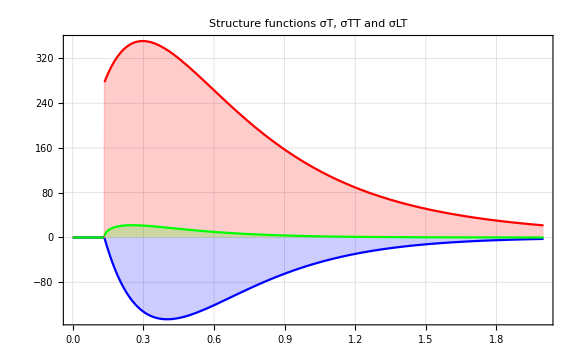

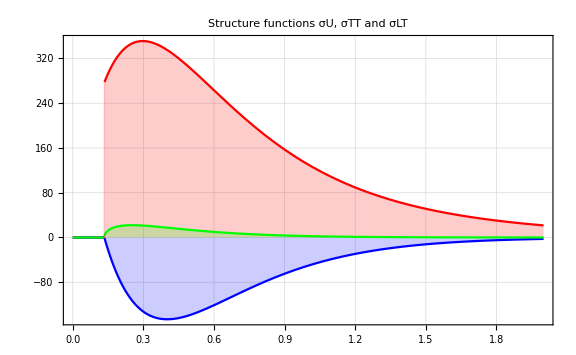

Placed::labpos: {Scaled[1],Before} is not a valid position for the placement of labels.

-Graphics-

Placed::labpos: {Scaled[1],Before} is not a valid position for the placement of labels.

-Graphics-

Placed::labpos: {Scaled[1],Before} is not a valid position for the placement of labels.

-Graphics-

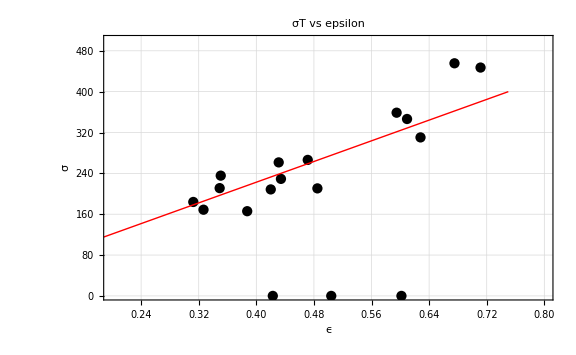

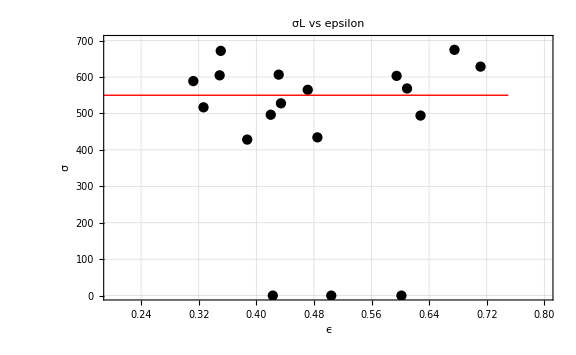

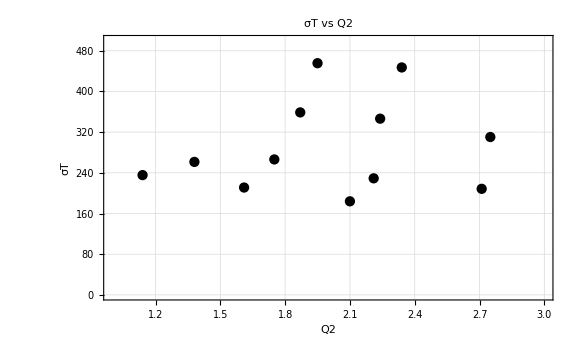

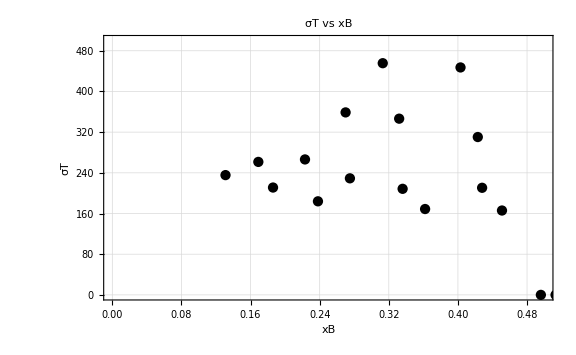

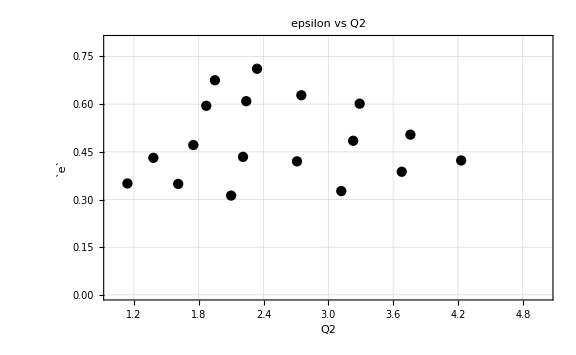

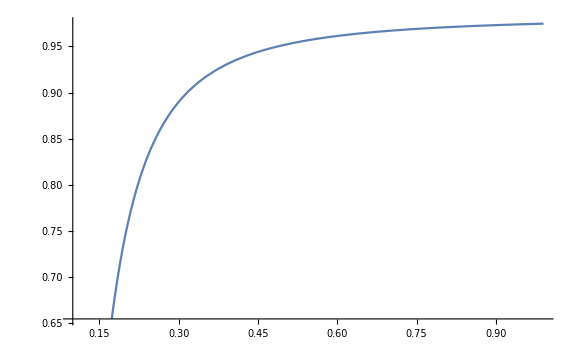

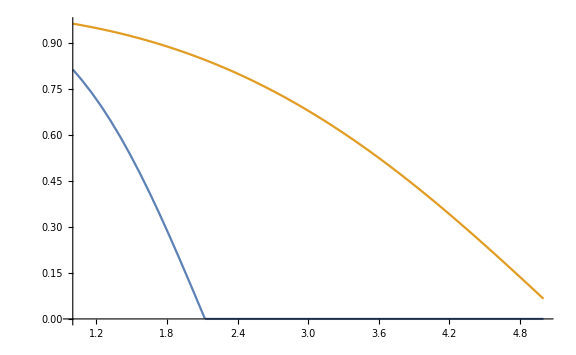

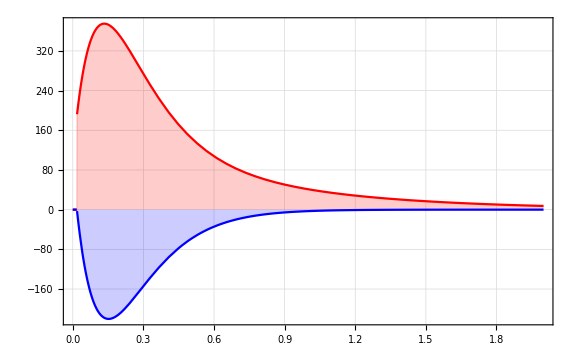

```mathematica
(*  --------------                        P L O T S                       ---------------*)


QQ2=2.24;
xB=0.332;
tt=-0.2;
Plot[{sT[-t,QQ2,xB],sTT[-t,QQ2,xB],sLT[-t,QQ2,xB]},{t,0.0,2.0},
Frame->True,Filling->Axis,PlotStyle->{Red,Blue,Green,Magenta},ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,PlotRange->All,
PlotLabel->"Structure functions σT, σTT and σLT"
(*PlotLegends->Placed[{"σT","σTT","σLT"},Left]*)
]
(* -----------------------------------------     *)
Plot[{sU[-t,QQ2,xB,Ebeam],sTT[-t,QQ2,xB],sLT[-t,QQ2,xB]},{t,0.0,2.0},
Frame->True,Filling->Axis,PlotStyle->{Red,Blue,Green,Magenta},ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,PlotRange->All,
PlotLabel->"Structure functions σU, σTT and σLT"
(*PlotLegends->Placed[{"σU","σTT","σLT"},Left]*)
]
(* -----------------------------------------     *)
QQ2=1.75;
xB=0.332;
Plot[{sU[-t,QQ2,xB,Eb],sTmin[-t,QQ2,xB],eps[QQ2,xB,Eb]sLmax[-t,QQ2,xB],sLmax[-t,QQ2,xB]},{t,0.0,2.0},
Frame->True,Filling->Axis,PlotStyle->{Red,Black,Magenta,Green,Magenta},ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,PlotRange->All,
PlotLabel->"(Q2=1.75, xB=0.332)",
PlotLegends->Placed[{"σ_U","σ_Tmin","ϵ σ_Lmax","σ_Lmax"},{Scaled[1],Before}]
]
(* -----------------------------------------     *)
QQ2=2.24;
xB=0.332;
Plot[{sU[-t,QQ2,xB,Eb],sTmin[-t,QQ2,xB],eps[QQ2,xB,Eb]sLmax[-t,QQ2,xB],sLmax[-t,QQ2,xB]},{t,0.0,2.0},
Frame->True,Filling->Axis,PlotStyle->{Red,Black,Magenta,Green,Magenta},ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,PlotRange->All,
PlotLabel->"(Q2=2.24, xB=0.332)",
PlotLegends->Placed[{"σ_U","σ_Tmin","ϵ σ_Lmax","σ_Lmax"},{Scaled[1],Before}]
]
Plot[{sU[T,QQ2,xB,Eb],sTmin[T,QQ2,xB],eps[QQ2,xB,Eb]sLmax[T,QQ2,xB],sLmax[T,QQ2,xB]},{xB,0.25,0.5},
Frame->True,Filling->Axis,PlotStyle->{Red,Blue,Magenta,Green,Magenta},ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,PlotRange->All,
PlotLabel->"(Q2=2.24, xB=0.332)",
PlotLegends->Placed[{"σ_U","σ_Tmin","ϵ σ_Lmax","σ_Lmax"},{Scaled[1],Before}]
]
(*========  PLOTS  ================*) 
Data=Transpose@{epsList,sTList};
lineStyle={Thick,Red};
line1=Line[{{0.0,20},{0.75,400.}}];
ListPlot[Data,
PlotLabel->"σT vs epsilon",FrameLabel->{"ϵ","σ"},
PlotStyle->{Black},Frame->True,
PlotStyle->{Directive[lineStyle]},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->{{0.2,0.8},{2.,500.}},
Epilog->{Directive[lineStyle],line1}
]
(* -----------------------------------------     *)
Data=Transpose@{epsList,sLnList};
lineStyle={Thick,Red};
line1=Line[{{0.,550},{0.75,550}}];
ListPlot[Data,
PlotLabel->"σL vs epsilon",
PlotStyle->{Black},
Frame->True,
FrameLabel->{"ϵ","σ"},
PlotStyle->{Directive[lineStyle]},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->{{0.2,0.8},{2,700.}},
Epilog->{Directive[lineStyle],line1}
]
(* -----------------------------------------     *)
Data2=Transpose@{Q2List,sTList};
ListPlot[Data2,
PlotLabel->"σT vs Q2",
PlotStyle->{Black},
Frame->True,
FrameLabel->{"Q2","σT"},
PlotStyle->{Directive[lineStyle]},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->{{1.,3.0},{0.,500.}}
]
(* -----------------------------------------     *)
Data2=Transpose@{xBList,sTList};
ListPlot[Data2,
PlotLabel->"σT vs xB",
PlotStyle->{Black},
Frame->True,
FrameLabel->{"xB","σT"},
PlotStyle->{Directive[lineStyle]},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->{{0.,0.5},{0.,500.}}
]
(* -----------------------------------------     *)
Data2=Transpose@{Q2List,epsList};
ListPlot[Data2,
PlotLabel->"epsilon vs Q2",
PlotStyle->{Black},
Frame->True,
FrameLabel->{"Q2","`e`"},
PlotStyle->{Directive[lineStyle]},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->{{1.,5.0},{0.,.8}}
]
(* -----------------------------------------     *)
QQ2=1.14;
xB=0.131;
tt=-0.2;
Plot[{eps[QQ2,x,Ebeam]},{x,0.1,0.99}]
Plot[{eps[Q2,0.2,Ebeam],eps[Q2,0.5,Ebeam]},{Q2,1.,5.}]
(*Plot[{tmin[QQ2,x]},{x,0.1,0.5}]
Plot[{sU[-t,QQ2,xB,Ebeam],sTT[-t,QQ2,xB]},{t,0.0,2.0},PlotRange->All]*)
Plot[{sU[-t,QQ2,xB,Ebeam],sTT[-t,QQ2,xB]},{t,0.0,2.0},
Frame->True,
Filling->Axis,
PlotStyle->{Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->All
]
```

```mathematica
DecimalForm[x,9]
```

```mathematica
QQ2=2.;xxB=0.23  
Plot[{eps[QQ2,xxB,e]},{e,6.5,10.6},PlotRange->All]
```

0.23

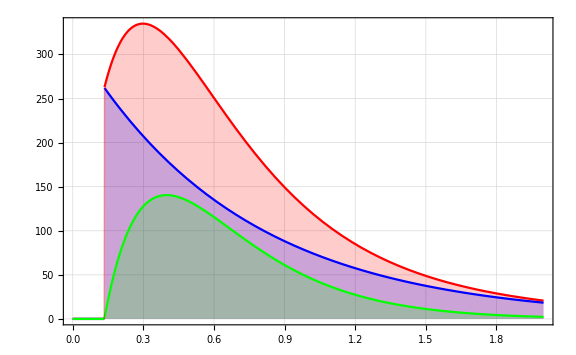

```mathematica
QQ2=2.24;
xB=0.332;
tt=-0.2;
Plot[{sT[-t,QQ2,xB],sT1[-t,QQ2,xB],sT2[-t,QQ2,xB]},{t,0.0,2.0},
Frame->True,
Filling->Axis,
PlotStyle->{Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->All
]
```

sTI[2.,0.2]

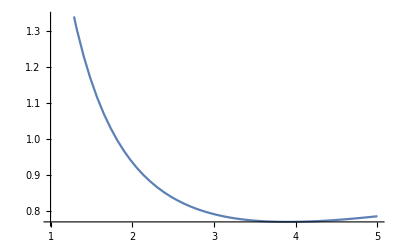

```mathematica
sTI[Q2,xB]:=NIntegrate[sT[-t,Q2,xB],{t,0.,.5}]; 
sTI[2.,0.2]
Plot[{NIntegrate[sT[-t,Q2,0.43],{t,0.,2.}]/(5410/Q2^(5.22/2))},{Q2,1.,5.}]
```

```mathematica
sTI[3.,0.34]
```

sTI[3.,0.34]